## Data

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="01_03_2022-04_02_2022.xls"
```

01_03_2022-04_02_2022.xls

### Import

```mathematica
importData=Import[dir<>xlsfile];
```

{{{記録時間,時間帯,血糖値,血圧,脈拍,体重,体脂肪率,食べ物とその量,薬,運動,気分,メモ},{2022-02-02 16:45:00,昼食後,379.,,,,,,,,,},{2022-02-03 06:13:00,起床,148.,,,,,,,,,},{2022-02-03 11:20:00,昼食前,396.,,,,,,,,,},{2022-02-03 16:36:00,昼食後,257.,,,,,,,,,},{2022-02-04 06:11:00,起床,177.,,,,,,,,,},{2022-02-04 11:16:00,昼食前,273.,,,,,,,,,},{2022-02-04 18:50:00,夕食前,204.,,,,,,,,,},{2022-02-05 05:57:00,深夜,98.,,,,,,,,,},{2022-02-05 12:11:00,昼食前,137.,,,,,,,,,},{2022-02-05 17:15:00,夕食前,226.,,,,,,,,,},{2022-02-06 06:08:00,起床,181.,,,,,,,,,},{2022-02-06 07:30:00,朝食後,84.,,,,,,,,,},{2022-02-06 12:20:00,昼食前,374.,,,,,,,,,},{2022-02-06 17:28:00,夕食前,241.,,,,,,,,,},{2022-02-07 06:17:00,起床,158.,,,,,,,,,},{2022-02-07 11:34:00,昼食前,293.,,,,,,,,,},{2022-02-07 16:44:00,昼食後,382.,,,,,,,,,},{2022-02-08 06:23:00,起床,152.,,,,,,,,,},{2022-02-08 12:09:00,昼食前,399.,,,,,,,,,},{2022-02-08 17:03:00,夕食前,275.,,,,,,,,,},{2022-02-09 05:51:00,深夜,116.,,,,,,,,,},{2022-02-09 11:54:00,昼食前,348.,,,,,,,,,},{2022-02-09 17:04:00,夕食前,271.,,,,,,,,,},{2022-02-10 06:12:00,起床,216.,,,,,,,,,},{2022-02-10 11:54:00,昼食前,133.,,,,,,,,,},{2022-02-10 17:01:00,夕食前,264.,,,,,,,,,},{2022-02-11 06:25:00,起床,191.,,,,,,,,,},{2022-02-11 12:00:00,昼食前,197.,,,,,,,,,},{2022-02-11 17:04:00,夕食前,224.,,,,,,,,,},{2022-02-12 06:23:00,起床,165.,,,,,,,,,},{2022-02-12 12:09:00,昼食前,210.,,,,,,,,,},{2022-02-12 17:09:00,夕食前,213.,,,,,,,,,},{2022-02-13 06:17:00,起床,217.,,,,,,,,,},{2022-02-13 12:27:00,昼食前,286.,,,,,,,,,},{2022-02-13 17:23:00,夕食前,300.,,,,,,,,,},{2022-02-14 06:12:00,起床,211.,,,,,,,,,},{2022-02-14 12:18:00,昼食前,245.,,,,,,,,,},{2022-02-14 18:49:00,夕食前,204.,,,,,,,,,},{2022-02-15 06:18:00,起床,199.,,,,,,,,,},{2022-02-15 11:59:00,昼食前,287.,,,,,,,,,},{2022-02-15 18:21:00,夕食前,205.,,,,,,,,,},{2022-02-16 06:15:00,起床,226.,,,,,,,,,},{2022-02-16 12:16:00,昼食前,308.,,,,,,,,,},{2022-02-16 18:27:00,夕食前,242.,,,,,,,,,},{2022-02-17 06:21:00,起床,238.,,,,,,,,,},{2022-02-17 12:07:00,昼食前,209.,,,,,,,,,},{2022-02-17 19:06:00,夕食後,210.,,,,,,,,,},{2022-02-18 06:11:00,起床,190.,,,,,,,,,},{2022-02-18 12:12:00,昼食前,288.,,,,,,,,,},{2022-02-18 19:21:00,夕食後,211.,,,,,,,,,},{2022-02-19 06:13:00,起床,231.,,,,,,,,,},{2022-02-19 12:17:00,昼食前,231.,,,,,,,,,},{2022-02-19 17:55:00,夕食前,179.,,,,,,,,,},{2022-02-20 06:52:00,起床,217.,,,,,,,,,},{2022-02-20 12:20:00,昼食前,243.,,,,,,,,,},{2022-02-20 17:42:00,夕食前,244.,,,,,,,,,},{2022-02-21 06:20:00,起床,197.,,,,,,,,,},{2022-02-21 12:07:00,昼食前,206.,,,,,,,,,},{2022-02-21 19:04:00,夕食後,195.,,,,,,,,,},{2022-02-22 06:36:00,起床,186.,,,,,,,,,},{2022-02-22 12:20:00,昼食前,208.,,,,,,,,,},{2022-02-22 19:44:00,夕食後,193.,,,,,,,,,},{2022-02-23 06:35:00,起床,224.,,,,,,,,,},{2022-02-23 12:00:00,昼食前,232.,,,,,,,,,},{2022-02-23 17:11:00,夕食前,194.,,,,,,,,,},{2022-02-24 06:29:00,起床,214.,,,,,,,,,},{2022-02-24 11:59:00,昼食前,233.,,,,,,,,,},{2022-02-24 19:31:00,夕食後,194.,,,,,,,,,},{2022-02-25 06:19:00,起床,224.,,,,,,,,,},{2022-02-25 12:26:00,昼食前,206.,,,,,,,,,},{2022-02-25 19:37:00,夕食後,188.,,,,,,,,,},{2022-02-26 06:24:00,起床,223.,,,,,,,,,},{2022-02-26 11:56:00,昼食前,261.,,,,,,,,,},{2022-02-26 18:00:00,夕食前,180.,,,,,,,,,},{2022-02-27 06:27:00,起床,208.,,,,,,,,,},{2022-02-27 12:14:00,昼食前,212.,,,,,,,,,},{2022-02-27 17:25:00,夕食前,161.,,,,,,,,,},{2022-02-28 06:31:00,起床,197.,,,,,,,,,},{2022-02-28 11:58:00,昼食前,221.,,,,,,,,,},{2022-02-28 18:32:00,夕食前,184.,,,,,,,,,},{2022-03-01 06:13:00,起床,195.,,,,,,,,,},{2022-03-01 12:08:00,昼食前,213.,,,,,,,,,},{2022-03-01 18:30:00,夕食前,173.,,,,,,,,,},{2022-03-02 06:29:00,起床,192.,,,,,,,,,},{2022-03-02 12:07:00,昼食前,239.,,,,,,,,,},{2022-03-02 18:40:00,夕食前,187.,,,,,,,,,},{2022-03-03 06:23:00,起床,177.,,,,,,,,,},{2022-03-03 12:32:00,昼食前,209.,,,,,,,,,},{2022-03-03 18:53:00,夕食前,209.,,,,,,,,,},{2022-03-04 12:15:00,昼食前,175.,,,,,,,,,},{2022-03-04 18:59:00,夕食前,173.,,,,,,,,,},{2022-03-05 06:18:00,起床,194.,,,,,,,,,},{2022-03-05 11:58:00,昼食前,163.,,,,,,,,,},{2022-03-05 18:01:00,夕食前,214.,,,,,,,,,},{2022-03-06 06:15:00,起床,145.,,,,,,,,,},{2022-03-06 12:24:00,昼食前,182.,,,,,,,,,},{2022-03-06 18:14:00,夕食前,195.,,,,,,,,,},{2022-03-07 06:16:00,起床,175.,,,,,,,,,},{2022-03-07 12:00:00,昼食前,214.,,,,,,,,,},{2022-03-07 18:52:00,夕食前,168.,,,,,,,,,},{2022-03-08 06:29:00,起床,162.,,,,,,,,,},{2022-03-08 12:48:00,昼食前,165.,,,,,,,,,},{2022-03-08 18:31:00,夕食前,172.,,,,,,,,,},{2022-03-09 06:09:00,起床,157.,,,,,,,,,},{2022-03-09 11:50:00,昼食前,202.,,,,,,,,,},{2022-03-09 18:26:00,夕食前,152.,,,,,,,,,},{2022-03-10 06:20:00,起床,168.,,,,,,,,,},{2022-03-10 12:07:00,昼食前,182.,,,,,,,,,},{2022-03-10 19:08:00,夕食後,144.,,,,,,,,,},{2022-03-11 06:06:00,起床,150.,,,,,,,,,},{2022-03-11 11:58:00,昼食前,161.,,,,,,,,,},{2022-03-11 18:11:00,夕食前,173.,,,,,,,,,},{2022-03-12 06:09:00,起床,132.,,,,,,,,,},{2022-03-12 12:42:00,昼食前,207.,,,,,,,,,},{2022-03-12 18:06:00,夕食前,262.,,,,,,,,,},{2022-03-13 06:24:00,起床,184.,,,,,,,,,},{2022-03-13 12:12:00,昼食前,170.,,,,,,,,,},{2022-03-13 18:07:00,夕食前,168.,,,,,,,,,},{2022-03-14 06:14:00,起床,154.,,,,,,,,,},{2022-03-14 11:59:00,昼食前,197.,,,,,,,,,},{2022-03-14 18:45:00,夕食前,134.,,,,,,,,,},{2022-03-15 06:13:00,起床,129.,,,,,,,,,},{2022-03-15 12:04:00,昼食前,133.,,,,,,,,,},{2022-03-15 18:25:00,夕食前,160.,,,,,,,,,},{2022-03-16 06:18:00,起床,142.,,,,,,,,,},{2022-03-16 12:02:00,昼食前,192.,,,,,,,,,},{2022-03-16 17:56:00,夕食前,145.,,,,,,,,,},{2022-03-17 06:18:00,起床,104.,,,,,,,,,},{2022-03-17 12:33:00,昼食前,173.,,,,,,,,,},{2022-03-17 18:28:00,夕食前,149.,,,,,,,,,},{2022-03-18 06:16:00,起床,124.,,,,,,,,,},{2022-03-18 12:42:00,昼食前,202.,,,,,,,,,},{2022-03-18 19:30:00,夕食後,144.,,,,,,,,,},{2022-03-19 06:27:00,起床,178.,,,,,,,,,},{2022-03-19 12:11:00,昼食前,164.,,,,,,,,,},{2022-03-19 18:11:00,夕食前,161.,,,,,,,,,},{2022-03-20 07:13:00,朝食前,159.,,,,,,,,,},{2022-03-20 12:11:00,昼食前,132.,,,,,,,,,},{2022-03-20 18:27:00,夕食前,147.,,,,,,,,,},{2022-03-21 06:34:00,起床,169.,,,,,,,,,},{2022-03-21 13:00:00,昼食前,192.,,,,,,,,,},{2022-03-21 18:22:00,夕食前,175.,,,,,,,,,},{2022-03-23 11:17:00,昼食前,183.,,,,,,,,,},{2022-03-23 16:49:00,昼食後,148.,,,,,,,,,},{2022-03-24 06:45:00,起床,183.,,,,,,,,,},{2022-03-24 11:56:00,昼食前,131.,,,,,,,,,},{2022-03-24 18:37:00,夕食前,130.,,,,,,,,,},{2022-03-25 06:12:00,起床,134.,,,,,,,,,},{2022-03-25 12:05:00,昼食前,134.,,,,,,,,,},{2022-03-25 21:36:00,就寝,114.,,,,,,,,,},{2022-03-26 09:09:00,朝食後,123.,,,,,,,,,},{2022-03-26 12:08:00,昼食前,108.,,,,,,,,,},{2022-03-26 18:43:00,夕食前,221.,,,,,,,,,},{2022-03-27 07:51:00,朝食前,185.,,,,,,,,,},{2022-03-27 12:41:00,昼食前,141.,,,,,,,,,},{2022-03-27 18:29:00,夕食前,180.,,,,,,,,,},{2022-03-28 07:40:00,朝食前,129.,,,,,,,,,},{2022-03-28 12:00:00,昼食前,132.,,,,,,,,,},{2022-03-28 18:49:00,夕食前,123.,,,,,,,,,},{2022-03-29 06:28:00,起床,124.,,,,,,,,,},{2022-03-29 12:06:00,昼食前,159.,,,,,,,,,},{2022-03-29 19:50:00,夕食後,122.,,,,,,,,,},{2022-03-31 07:15:00,朝食前,141.,,,,,,,,,},{2022-03-31 12:04:00,昼食前,128.,,,,,,,,,},{2022-03-31 18:02:00,夕食前,274.,,,,,,,,,},{2022-04-02 06:47:00,起床,90.,,,,,,,,,},{2022-04-02 12:42:00,昼食前,143.,,,,,,,,,},{2022-04-02 18:11:00,夕食前,105.,,,,,,,,,}}}

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

{{2022-02-02 16:45:00,379.},{2022-02-03 06:13:00,148.},{2022-02-03 11:20:00,396.},{2022-02-03 16:36:00,257.},{2022-02-04 06:11:00,177.},{2022-02-04 11:16:00,273.},{2022-02-04 18:50:00,204.},{2022-02-05 05:57:00,98.},{2022-02-05 12:11:00,137.},{2022-02-05 17:15:00,226.},{2022-02-06 06:08:00,181.},{2022-02-06 07:30:00,84.},{2022-02-06 12:20:00,374.},{2022-02-06 17:28:00,241.},{2022-02-07 06:17:00,158.},{2022-02-07 11:34:00,293.},{2022-02-07 16:44:00,382.},{2022-02-08 06:23:00,152.},{2022-02-08 12:09:00,399.},{2022-02-08 17:03:00,275.},{2022-02-09 05:51:00,116.},{2022-02-09 11:54:00,348.},{2022-02-09 17:04:00,271.},{2022-02-10 06:12:00,216.},{2022-02-10 11:54:00,133.},{2022-02-10 17:01:00,264.},{2022-02-11 06:25:00,191.},{2022-02-11 12:00:00,197.},{2022-02-11 17:04:00,224.},{2022-02-12 06:23:00,165.},{2022-02-12 12:09:00,210.},{2022-02-12 17:09:00,213.},{2022-02-13 06:17:00,217.},{2022-02-13 12:27:00,286.},{2022-02-13 17:23:00,300.},{2022-02-14 06:12:00,211.},{2022-02-14 12:18:00,245.},{2022-02-14 18:49:00,204.},{2022-02-15 06:18:00,199.},{2022-02-15 11:59:00,287.},{2022-02-15 18:21:00,205.},{2022-02-16 06:15:00,226.},{2022-02-16 12:16:00,308.},{2022-02-16 18:27:00,242.},{2022-02-17 06:21:00,238.},{2022-02-17 12:07:00,209.},{2022-02-17 19:06:00,210.},{2022-02-18 06:11:00,190.},{2022-02-18 12:12:00,288.},{2022-02-18 19:21:00,211.},{2022-02-19 06:13:00,231.},{2022-02-19 12:17:00,231.},{2022-02-19 17:55:00,179.},{2022-02-20 06:52:00,217.},{2022-02-20 12:20:00,243.},{2022-02-20 17:42:00,244.},{2022-02-21 06:20:00,197.},{2022-02-21 12:07:00,206.},{2022-02-21 19:04:00,195.},{2022-02-22 06:36:00,186.},{2022-02-22 12:20:00,208.},{2022-02-22 19:44:00,193.},{2022-02-23 06:35:00,224.},{2022-02-23 12:00:00,232.},{2022-02-23 17:11:00,194.},{2022-02-24 06:29:00,214.},{2022-02-24 11:59:00,233.},{2022-02-24 19:31:00,194.},{2022-02-25 06:19:00,224.},{2022-02-25 12:26:00,206.},{2022-02-25 19:37:00,188.},{2022-02-26 06:24:00,223.},{2022-02-26 11:56:00,261.},{2022-02-26 18:00:00,180.},{2022-02-27 06:27:00,208.},{2022-02-27 12:14:00,212.},{2022-02-27 17:25:00,161.},{2022-02-28 06:31:00,197.},{2022-02-28 11:58:00,221.},{2022-02-28 18:32:00,184.},{2022-03-01 06:13:00,195.},{2022-03-01 12:08:00,213.},{2022-03-01 18:30:00,173.},{2022-03-02 06:29:00,192.},{2022-03-02 12:07:00,239.},{2022-03-02 18:40:00,187.},{2022-03-03 06:23:00,177.},{2022-03-03 12:32:00,209.},{2022-03-03 18:53:00,209.},{2022-03-04 12:15:00,175.},{2022-03-04 18:59:00,173.},{2022-03-05 06:18:00,194.},{2022-03-05 11:58:00,163.},{2022-03-05 18:01:00,214.},{2022-03-06 06:15:00,145.},{2022-03-06 12:24:00,182.},{2022-03-06 18:14:00,195.},{2022-03-07 06:16:00,175.},{2022-03-07 12:00:00,214.},{2022-03-07 18:52:00,168.},{2022-03-08 06:29:00,162.},{2022-03-08 12:48:00,165.},{2022-03-08 18:31:00,172.},{2022-03-09 06:09:00,157.},{2022-03-09 11:50:00,202.},{2022-03-09 18:26:00,152.},{2022-03-10 06:20:00,168.},{2022-03-10 12:07:00,182.},{2022-03-10 19:08:00,144.},{2022-03-11 06:06:00,150.},{2022-03-11 11:58:00,161.},{2022-03-11 18:11:00,173.},{2022-03-12 06:09:00,132.},{2022-03-12 12:42:00,207.},{2022-03-12 18:06:00,262.},{2022-03-13 06:24:00,184.},{2022-03-13 12:12:00,170.},{2022-03-13 18:07:00,168.},{2022-03-14 06:14:00,154.},{2022-03-14 11:59:00,197.},{2022-03-14 18:45:00,134.},{2022-03-15 06:13:00,129.},{2022-03-15 12:04:00,133.},{2022-03-15 18:25:00,160.},{2022-03-16 06:18:00,142.},{2022-03-16 12:02:00,192.},{2022-03-16 17:56:00,145.},{2022-03-17 06:18:00,104.},{2022-03-17 12:33:00,173.},{2022-03-17 18:28:00,149.},{2022-03-18 06:16:00,124.},{2022-03-18 12:42:00,202.},{2022-03-18 19:30:00,144.},{2022-03-19 06:27:00,178.},{2022-03-19 12:11:00,164.},{2022-03-19 18:11:00,161.},{2022-03-20 07:13:00,159.},{2022-03-20 12:11:00,132.},{2022-03-20 18:27:00,147.},{2022-03-21 06:34:00,169.},{2022-03-21 13:00:00,192.},{2022-03-21 18:22:00,175.},{2022-03-23 11:17:00,183.},{2022-03-23 16:49:00,148.},{2022-03-24 06:45:00,183.},{2022-03-24 11:56:00,131.},{2022-03-24 18:37:00,130.},{2022-03-25 06:12:00,134.},{2022-03-25 12:05:00,134.},{2022-03-25 21:36:00,114.},{2022-03-26 09:09:00,123.},{2022-03-26 12:08:00,108.},{2022-03-26 18:43:00,221.},{2022-03-27 07:51:00,185.},{2022-03-27 12:41:00,141.},{2022-03-27 18:29:00,180.},{2022-03-28 07:40:00,129.},{2022-03-28 12:00:00,132.},{2022-03-28 18:49:00,123.},{2022-03-29 06:28:00,124.},{2022-03-29 12:06:00,159.},{2022-03-29 19:50:00,122.},{2022-03-31 07:15:00,141.},{2022-03-31 12:04:00,128.},{2022-03-31 18:02:00,274.},{2022-04-02 06:47:00,90.},{2022-04-02 12:42:00,143.},{2022-04-02 18:11:00,105.}}

### SemanticImport

```mathematica
semanticData=SemanticImport[dir<>xlsfile]
```

```mathematica
semantic["date","glu"]=Map[{#[[1]],#[[3]]}&,semanticData]
```

```mathematica
semantic["date"]=Map[#[[1]]&,semanticData]
```

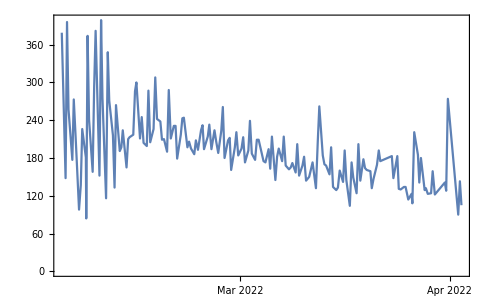

```mathematica
DateListPlot[semantic["date","glu"]]
```

```mathematica
semantic["date"]
```

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
DateList[semantic["date"][[1]]]
```

```mathematica
AbsoluteTime[semantic["date"][[1]]]
```

3852809100

```mathematica
DateList[semantic["date"][[1]]]
```

```mathematica
AbsoluteTime[semantic["date"]]
```

AbsoluteTime::arg: 引数Dataset[«168»]は日付または時間入力として解釈することができません．

AbsoluteTime[]